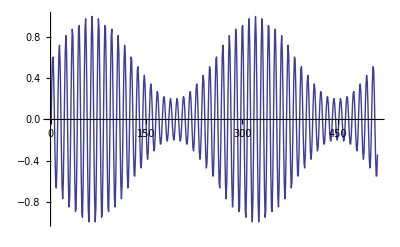

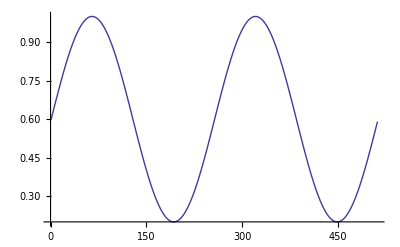

```mathematica
sinus=Table[Sin[2π 50 t/512],{t,0,511}];
ListPlot[sinus*LFO, Joined-> True]
LFO=Table[0.4Sin[2π 2 t/512]+0.6,{t,0,511}];
ListPlot[LFO, Joined-> True]
```

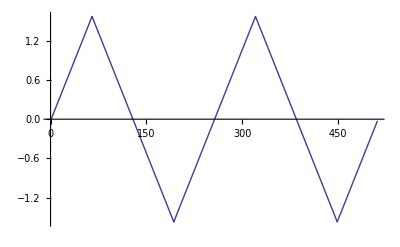

```mathematica
sinus2=Table[Sin[2π 2 t/512],{t,0,511}];
ListPlot[ArcSin[sinus2], Joined-> True]
```

```mathematica
sinus1=Table[1/1 Sin[2π 2 t/512],{t,0,511}];
sinus2=Table[1/2 Sin[2π 4 t/512],{t,0,511}];
sinus3=Table[1/3 Sin[2π 6 t/512],{t,0,511}];
sinus4=Table[1/4 Sin[2π 8 t/512],{t,0,511}];
sinus5=Table[1/5 Sin[2π 10 t/512],{t,0,511}];
ListPlot[{sinus1,sinus2,sinus3,sinus4,sinus5} ,Joined-> True]
```